# Binomial series examples

Katharine Long, Texas Tech University

### Some simple binomial series

```mathematica
Series[(1+x)^(-1/2),{x,0,6}]
```

1-x/2+(3 x^2)/8-(5 x^3)/16+(35 x^4)/128-(63 x^5)/256+(231 x^6)/1024+O(x^7)

```mathematica
Series[(1+x)^(1/8),{x,0,6}]
```

1+x/8-(7 x^2)/128+(35 x^3)/1024-(805 x^4)/32768+(4991 x^5)/262144-(64883 x^6)/4194304+O(x^7)

```mathematica
Series[(1+x)^(5/3),{x,0,6}]
```

1+(5 x)/3+(5 x^2)/9-(5 x^3)/81+(5 x^4)/243-(7 x^5)/729+(35 x^6)/6561+O(x^7)

### Use “Normal” to convert the series into a polynomial

```mathematica
g[n_,x_]:=Normal[Series[(1+x)^(-1/2),{x,0,n}]]
```

```mathematica
g2[x_]=g[2,x];g4[x_]=g[4,x]; g8[x_]=g[8,x]; g16[x_]=g[16,x];
```

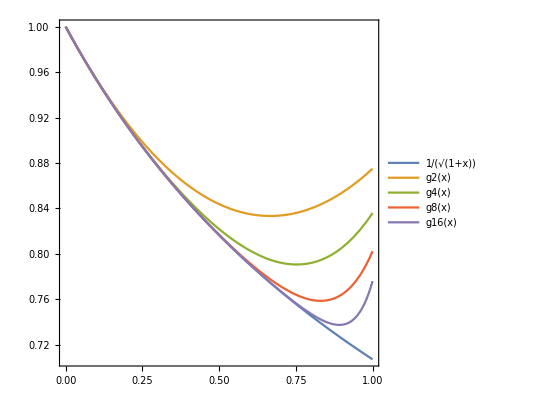

```mathematica
Plot[{1/Sqrt[1+x],g2[x],g4[x],g8[x],g16[x]},{x,0,1},PlotLegends->Placed["Expressions",{0.7,0.7}],AspectRatio->1,PlotRange->{1/Sqrt[2],1}]
```

### An example from relativity

Relativistic kinetic energy

```mathematica
KE = Subscript[m, 0] c^2/Sqrt[1-v^2/c^2]
```

(c^2 m_0)/(√(1-v^2/c^2))

#### Expand about v=0

Through power v^2 gives the classical kinetic energy

```mathematica
Series[KE, {v,0,2}]
```

c^2 m_0+(m_0 v^2)/2+O(v^3)

Higher order terms are needed as v→ c

```mathematica
Series[KE,{v,0,6}]
```

c^2 m_0+(m_0 v^2)/2+(3 m_0 v^4)/(8 c^2)+(5 m_0 v^6)/(16 c^4)+O(v^7)

#### Example: 1/√(x+y)

Case x << y

```mathematica
Expand[Sqrt[y]Normal[Series[(x+y)^(-1/2),{x, 0, 3}]]]/Sqrt[y]
```

(-(5 x^3)/(16 y^3)+(3 x^2)/(8 y^2)-x/(2 y)+1)/(√y)

Case y<< x

```mathematica
Expand[Sqrt[x]Normal[Series[(x+y)^(-1/2),{y, 0, 3}]]]/Sqrt[x]
```

(-(5 y^3)/(16 x^3)+(3 y^2)/(8 x^2)-y/(2 x)+1)/(√x)

### Example: Plummer’s potential for globular star cluster

r is distance from the cluster’s center

```mathematica
Φ[r_]=-G M / Sqrt[a^2 + r^2]
```

-(G M)/(√(a^2+r^2))

#### Behavior at large r (r>> a) Use powers of a

```mathematica
Expand[PowerExpand[Normal[Series[Φ[r],{a,0,4}]]]]
```

-(3 a^4 G M)/(8 r^5)+(a^2 G M)/(2 r^3)-(G M)/r

Leading term is point-mass potential. Further terms improve the approximation.

#### Behavior at small r (r<<a). Use powers of r

```mathematica
Expand[PowerExpand[Normal[Series[Φ[r],{r,0,2}]]]]
```

(G M r^2)/(2 a^3)-(G M)/a

This is a harmonic oscillator potential. To improve the approximation, take more terms.

```mathematica
Expand[PowerExpand[Normal[Series[Φ[r],{r,0,6}]]]]
```

(5 G M r^6)/(16 a^7)-(3 G M r^4)/(8 a^5)+(G M r^2)/(2 a^3)-(G M)/a